# Physics 230 -- Lab 4 (Advanced Graphics)

## Branton J. Campbell, BYU Physics & Astronomy, Fall 2010 Steve Turley, BYU Physics & Astronomy, Fal 2011

When studying a complicated physical system, it is often helpful to build a graphical model that illustrates its essential features.  In this lab, we will learn how to build up complicated graphics objects from simpler building blocks called primitives, how to combine multiple graphics objects (even plots) together, and how to build dynamic behavior and interactivity into graphics objects.  We will then apply these tools to some basic physics problems.

Graphics, especially in 3D, involves a lot of detail.  This lab only touches the surface of some of Mathematica’s rich capabilities in this area to give you some ideas of what you can do.

## Working with the Drawing Tool (15 min)

A lot of the drawing illustrated in the following sections can be most easiler done using the Graphics Tool.  Using the Graphics Menu, you can create a Graphic in an input box such as the one below.
-Graphics-
This is essentially a canvass where you can draw whatever you want using the Drawing Tools which can be accessed using the Graphics Menu as well.  In the box below, I have illustrated some of the possibilities.

These graphics objects are not limited to graphics in input boxes.  They can also be used to label plots and other figures you have produced in output boxes.  Consider the following example.  After creating the ListPlot, I used the Drawing Tools to provide an annotation in the plot.

```mathematica
ListPlot[{{1,5},{1.5,6},{2,7},{2.5,8},{3,-2},{3.5,9},{4,10}},PlotStyle->PointSize[0.02], PlotRange->{{0.5,4.5},{-4,11}}]
```

The graphics items you add to the plot are individual objects that can be moved, resized, restyled, and deleted.  They can also be placed in front of or behind other objects and have various layers of transparency (opacity).  Using the operations tab, you’ll note that Mathematica also supplies tools to align, group, and distribute objects in various ways.

### (#1) Producing a Drawing (15 min)

Practice using the graphics tools to reproduce the following drawing as closely as you can.  I used 14 point Verdana as the text.  Use the alignment and distribute tools to align the buttons on the multichannel analyzer and make them equally spaced.
-Graphics-

## Working with raw Graphics primitives (45 min)

In the DC guide page on Mathematica's Symbolic Graphics Language, the first two links point to Graphics and Graphics3D.  These are very important and very general tools capable of rendering a wide variety of graphics.  Take a few minutes to walk through their DC reference pages, looking briefly at each of the major sections along the way.

The advantage of working with these primitives instead of the Drawing Tool is that you can program their location using Mathematica expressions and animate where they go.  For visually drawing static picture you will often find the Drawing Tool more convenient.

### (#2) Basic 2D graphics primitives (10 min)

(a) Circle is a "graphics primitive".  When a primitive is evaluated by itself, nothing much happens.  Try it.

```mathematica
Circle[]
```

Circle[{0,0}]

(b) The Graphics function can be used to "render" primitives as "graphics objects" on your computer screen.  In other words, it converts a set of primitives into a 2D image.  Evaluate the example below.



```mathematica
Graphics[Circle[]]
```

(c) It is important to understand something about the coordinates used for specifying the shapes and locations of primitives.  Evaluate the following example, and explain the output to your TA.

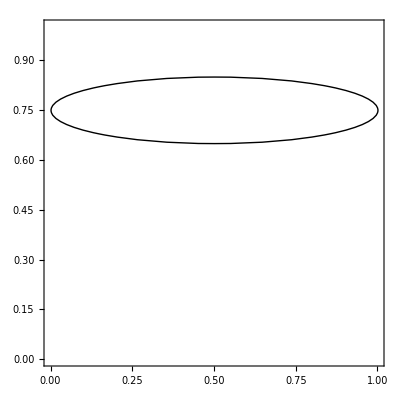

```mathematica
Graphics[Circle[{0.5,0.75},{0.5,0.1}],PlotRange->{{0,1},{0,1}},Frame->True]
```

(d) In general, Graphics can take an arbitrarily nested list containing any number of primitives.

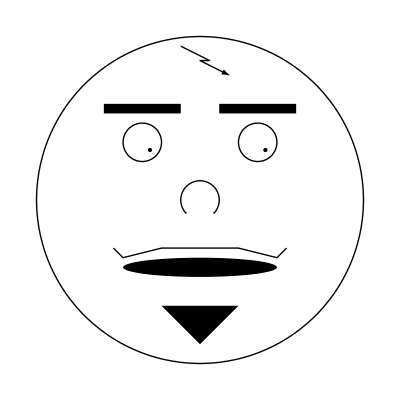

```mathematica
eyes = {Circle[{0.3,0.3},0.1],Circle[{-0.3,0.3},0.1],Point[{0.34,0.26}],Point[{-0.26,0.26}]};
eyebrows = {Rectangle[{-0.5,0.45},{-0.1,0.5}], Rectangle[{0.1,0.45},{0.5,0.5}]};
nose = Circle[{0,0},0.1,{-Pi/4,5Pi/4}];
mouth = Disk[{0,-0.35},{0.4,0.05}];
beard = Polygon[{{0,-0.75},{-0.2,-0.55},{0.2,-0.55}}];
mustache = Line[{{-0.45,-0.25},{-0.4,-0.3},{-0.2,-0.25},{0.2,-0.25},{0.4,-0.3},{0.45,-0.25}}];
scar = Arrow[{{-0.1,0.8},{0.05,0.725},{0,0.725},{0.15,0.65}}];
head = Circle[{0,0},0.85];

primitives = {head, eyes, eyebrows, nose,mouth,beard,mustache,scar};
Graphics[primitives]
```

(e) Create a graphic of your own that includes at least one instance of each of the following primitives: Point, Line, Circle, Disk and Rectangle.  Be a little creative; but don't spend too much time on it.

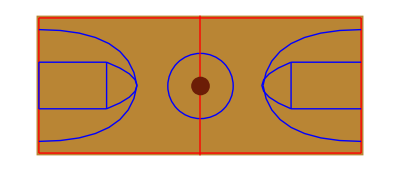

```mathematica
court ={RGBColor[185/255,133/255,52/255], Rectangle[{0.5,0.5},{7.5,3.5}]};
center = {Blue,Circle[{4,2},.7]};
halfCourt = {Red,Line[{{4,0.5},{4,3.5}}]};
boundaries = {{Red,Line[{{.55,3.45},{7.45,3.45}}],Line[{{.55,.55},{7.45,.55}}],Line[{{.55,3.45},{.55,.55}}],Line[{{7.45,3.45},{7.45,.55}}]}};
ball = {RGBColor[108/255,29/255,6/255],Disk[{4,2},.2]};
leftPost ={{Blue,Line[{{.55,1.5},{.55,2.5}}],Line[{{.55,1.5},{2,1.5}}],Line[{{.55,2.5},{2,2.5}}],Line[{{2,1.5},{2,2.5}}]}};
rightPost = {{Blue,Line[{{5.95,1.5},{7.45,1.5}}],Line[{{5.95,1.5},{5.95,2.5}}],Line[{{5.95,2.5},{7.45,2.5}}],Line[{{7.45,1.5},{7.45,1.5}}]}};
leftCircle = {Blue,BezierCurve[{{2,2.5},{3.3,2},{2,1.5}}]};
rightCircle={Blue,BezierCurve[{{5.95,2.5},{4.7,2},{5.95,1.5}}]};
leftThree = {Blue,BezierCurve[{{.55,3.2},{2.5,3.2},{2.65,2}}],BezierCurve[{{.55,.8},{2.5,.8},{2.65,2}}]};
rightThree = {Blue,BezierCurve[{{7.45,3.2},{5.5,3.2},{5.35,2}}],BezierCurve[{{7.45,.8},{5.5,.8},{5.35,2}}]};
Graphics[{court,center, halfCourt,boundaries,ball,leftPost,rightPost,leftCircle,rightCircle,leftThree,rightThree}]
```

### (#2) Basic 3D graphics primitives (10 min)

(a) In the cell below, we demonstrate the use of several 3D primitives: Cuboid, Sphere, Cylinder, Cone, Tube, Arrow and Polygon. Like the 3D plots that you have seen in the past, Graphics3D output can be interactively rotated with the mouse.  Evaluate and modify the example below.  You may want to refer to the appropriate DC reference pages for the definitions of the coordinates used by each type of primitive.

```mathematica
primitives = {Cylinder[{{1,1,0},{-1,-1,0}},0.5],Sphere[{0,0,1}],Cuboid[{-1,-1,-1},{1,1,0}], Polygon[{{1,1,-4},{-1,-1,-4},{0,0,4}}]}
Graphics3D[primitives]
```

(b) Create your own Graphics3D example in the next cell.  Be a little creative; but don't spend too much time on it.

### (#3) Options and directives for graphics primitives (5 min)

You probably noticed that graphics primitives work with most of the same options and directives that you encountered in the context of Plot and Plot3D.  There are, however, a few special directives like  EdgeForm and FaceForm, that are specific to primitives.  If you don't yet understand the difference between Graphics Options and Graphics Directives, now is the time to figure it out.  Directives are generally grouped together with the primitives, and only affect the primitives that follow them within the same group.  Options are applied at wrapping time in an option → setting format.  It is often possible, however, to include directives as the setting for an option.  In BoxStyle → Red, for example, the option is BoxStyle, and the directive, Red, is the setting.

Evaluate the following cell, and explain to your TA how options and directives are employed to modify the appearance of the plot.  Remember that a directive only affects the primitives that follow it in the list.

```mathematica
primitives = {Cylinder[{{0,0,-1},{0,0,1}},0.75],Sphere[{0,0,0},1]};
directives ={EdgeForm[{Thickness[0.01],Blue}],FaceForm[Orange],Specularity[White,20]};
options = {PlotRange->{{-1,1},{-1,1},{-1,1}}, BoxStyle->{Thick,Red}, BoxRatios->{1,1,1},Axes->True, FaceGrids->{{0,0,-1},{0,0,1}}, Lighting->"Neutral",SphericalRegion->True,ImageSize->300};

primitivesanddirectives = Join[directives,primitives]

Graphics3D[primitives]
Graphics3D[primitivesanddirectives]
Graphics3D[primitivesanddirectives,options]
```

### (#4) Geometric transformations (5 min)

See the DC guide page on Graphics Transformations, where the simplest examples appear at the top: Rotate, Scale and Translate.  Evaluate the cell below to see how transformations can alter the orientation, shape, size and position of a simple cube.  Explain to your TA what each of the following coordinate transformations does.  You will need to explain the coordinates inside of each transformation.

```mathematica
cube1 = Cuboid[{-1/4,-1/4,-1/4},{1/4,1/4,1/4}];
cube2 = Translate[cube1,{1/Sqrt[2],0,0}]; (* slide a distance of 1/Sqrt[2] along the +x direction *)
cube3= Rotate[cube2,Pi/4,{0,0,1},{0,0,0}]; (* 45 degree z-axis rotation around the origin *)
cube4= Scale[cube3,{1/2,1/2,2},{1/2,1/2,0}];  (* stretch along z and shrink along x and y *)

options = {Axes->True,AxesLabel->(Style[#,Large]&/@{"x","y","z"}),PlotRange->{{-1,1},{-1,1},{-1/2,1/2}},Lighting->"Neutral",
ViewPoint->{0,0,10},ViewVertical->{0,0,1}};

primitivesanddirectives = {{Red,cube1},{Blue,cube2},{Pink,cube3},{Green,cube4}};
Graphics3D[primitivesanddirectives,options]
```

### (#5) Combining rendered graphics objects (5 min)

(a)  Evaluate the cell below to create and render two graphics primitives.

```mathematica
p1 = Circle[];
p2 = Rectangle[];
g1 =  Graphics[p1]
g2 = Graphics[p2]
```

(b) Recall that you can always place multiple primitives in the same plot by grouping them in a list before rendering them as "graphics objects" them with Graphics or Graphics3D.  But once you have rendered two graphics, can the resulting objects still be combined into a single graph?.  Evaluate the cells below to test a few possible approaches.  Study the output (and any error messages) and explain what goes wrong to your TA?  View the FullForm output from each approach for clues.

```mathematica
{g1,g2}
%//FullForm

Graphics[{g1,g2}]
%//FullForm
```

(c)  Evaluate the cell elow to see two other possibilities.  First, you can reach inside the graphics objects, g1 and g2, to extract their primitives, and then recombine them into a single list.  Or you can use the Show function to conveniently accomplish the same thing.  If "How do we combine graphics objects?" is the question, then "Show" is the answer?

```mathematica
Graphics[{g1[[1]],g2[[1]]}]
%//FullForm

Show[g1,g2]
%//FullForm
```

### (#6) Combining plots and other graphics objects (5 min)

(a) We mentioned earlier that primitives and plots use many of the same options and directives.  These similarities are fundamental rather than superficial, since each of Mathematica's plotting functions actually outputs a Graphics or Graphics3D object containing a list of primitives.  Pause and read that last statement again. Then evaluate the example below, and compare the FullForm output from Graphics to that of Plot.

```mathematica
g1 = Graphics[{Circle[{0,0.5},0.5],Circle[{0,0.5},0.25]}];
g1//FullForm
g2= Plot[x^2,{x,-1,1}];
g2//FullForm
```

The take-home message here is that functions like Plot were designed to generate all of the primitives required to display the points, lines, surfaces, axes, ticks, grids and labels that make a graph look nice.  But at the end of the day, the output is still a graphics object full of primitives that you could have generated manually with enough time and effort.

(b) Because Plot and Graphics output are both graphics objects containing primitives, we can use Show to combine them into a single graph.  Try it.  Observe that the order (i.e. which one renders on top) affects the output.  Adding a few options further improves the result.

```mathematica
Show[g1,g2]
Show[g2,g1]
Show[{g2,g1},PlotRange->All,AspectRatio->Automatic,Frame->True,Axes->False]
```

(c) Create your own example that combines multiple 2D plots and graphics primitives into a single graph.

(d) The DC guide page on Combining Graphics contains links to several other functions that can be useful for combining graphics.  Take a quick look at Inset, Prolog and Epilog.

### (#7) Arrays of graphics (5 min)

The DC guide page on Combining Graphics contains links to several functions for creating grid-like arrays of graphics.  Follow the links to GraphicsGrid, GraphicsRow and GraphicsColumn to see how these functions are used.  Use GraphicsGrid and Partition to turn the following list of colored disks into a grid with 3 rows and 4 columns.

```mathematica
spots =  Table[Graphics[{EdgeForm[{Thick,Black}],Hue[n/12],Disk[]},ImageSize->50],{n,12}]
```

### 3D Camera views (optional)

Browse the DC guide page on 3D Graphics Options, where you will see a variety of options that control the position and angle from which a graphic is viewed, including ViewPoint, ViewCenter, ViewVertical and ViewAngle.  To understand these options, imagine that you, the observer, are using a camera to capture images of the 3D object contained in the graphic.  When the mouse is employed to rotate the figure, the object actually remains stationary, while you and the camera fly around the room seeing the object from different positions and angles.  Dizzy yet?  To summarize, these options allow us to exactly specify the view that we want rather than using the mouse to obtain an approximate view.

Evaluate the cell below and make each of the following modifications.
(a) Change the direction of the ViewPoint vector (but not the prefactor).  What happens?  Consider that normal mouse-click/drag operations also change the direction of the ViewPoint.
(b) Make the magnitude of the ViewPoint smaller and/or larger.  What happens?  Note that you can't achieve this effect with the mouse.
(c) Vary the ViewVertical direction slightly.  What does it do?  Move the mouse to a corner of the plot and see that the cursor changes to a circular arrow with a dot in the middle.  Using this new cursor, perform a mouse-click/drag operation.  This is equivalent to changing ViewVertical.
(d) Change the first ViewCenter vector to {0,0,0}, rotate the graph with your mouse to see the effect, and describe what happened.  Note that you can't achieve this kind of change with the mouse.  Then set the first vector back to {1/2,1/2,1/2} and the change the second ViewCenter vector to {1/2,0}, which represents a point within the 2D viewing window.  Rotate the graph with your mouse to see the effect and describe what happened.  This is equivalent to panning the graphic by holding down the Shift key while performing a mouse-click/drag.  Set the second vector back to {1/2,1/2}.
(e) Zoom in and out by holding the Ctrl key down while performing a mouse-click/drag.  Check that this is equivalent to varying the ViewAngle (the angular range that you want to see in the viewing window at a fixed camera distance from the object).  Increasing ViewAngle takes in a wider view of the world and consequently reduces the apparent size of the object in the view window, even though the distance to the object didn't change.  Though a little weird, this is a pretty basic computer graphics concept.
(f) Set the ViewAngle to Automatic, which is the normal default setting.  This automatically readjusts the ViewAngle whenever the ViewPoint distance changes so that the object always nicely fills most of the viewing window.  To see this, set the ViewPoint direction to {1,0,0} and its magnitude to 2.5.  Then change the magnitude to 100 and describe how the graph changes.  The effect is called "perspective" -- as you get closer to the object, the front of the box appears to be larger than the back.

```mathematica
plotoptions1 = {Axes->True,AxesLabel->{"x","y","z"},AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},PlotRange->{{-1,1},{-1,1},{-1,1}},SphericalRegion->True};
plotoptions2 = {ViewPoint->5*Normalize[{1,0,0}],ViewVertical->{0,1,0}, ViewCenter->{{1/2,1/2,1/2},{1/2,1/2}},ViewAngle->30 Degree};
Graphics3D[Scale[Sphere[],{1,0.75,0.5},{0,0,0}],plotoptions1,plotoptions2]
```

## Interactive graphics (30 min)

The DC homepage devotes an entire section to dynamic interactivity.  As of version 8.0, this is a large and rather complicated branch of Mathematica development.  The documentation on this material, while well organized, tends to be quite advanced.  Take a brief look at the guide pages on Dynamic Visualization and Interactive Manipulation, and observe that the first few links on both pages are the same.  We will only cover these three functions: Manipulate, Animate and ListAnimate.

### (#8-#10) Manipulation (15 min)

The DC has an excellent intro-level tutorial called Introduction to Manipulate, that will walk you step by step through a variety examples of the Manipulate function.  After opening this tutorial, take a moment to close each of the subsections so that you can easily scan the list topics covered.  Then spend about 30 minutes working through the entire tutorial.  Pace yourself.

#### (#8) Manipulating the Maxwell Distribution (5 min)

The Manipulate function allows you to interactively change the value of variables to see their result.  It is frequently used with graphics to illustrate how changing various parameters change the nature of the graph.  For example, consider the MaxwellDistribution function which describes the velocity distribution of particles in an ideal gas at various temperatures.  If  particle has a mass m and the gas is at a temperature T, the probability of an atom in the gas having a speed between v and v+dv is MaxwellDistribution[σ][v], where σ^2=kT/m, with k being Boltzmann’s constant.

Evaluate the following cell and use the slider to explore how the velocity distribution for helium changes as you vary the standard deviation using Manipulate.

```mathematica
k=1.38*10^-23;
m=4*1.66*10^-27;
σ[T_] = Sqrt[k*T/m];
Manipulate[Plot[PDF[MaxwellDistribution[σ[T]]][v],{v,0,3000}, PlotRange->{All,{0,0.006}},
PlotLabel->T " K", AxesLabel->{"speed (m/s)","probability density"}], {T,5,300}]
```

At what temperature is the most probable speed equal to 500 meters/second?

Answer:

#### (#9) Manipulating Trajectory of a Ball with Friction (5 min)

You learned in Physics 121 that an object in ballistic motion (moving only under the influence of gravity) will have a maximum range if it is thrown at an angle of 45 degrees.  The function trajectory below plots the trajectory of a ball which has air friction.  Under these conditions, there are two forces on the ball, gravity pulling the ball down with a force m*g and a drag force of -αmv^2 in the opposite direciton of the motion.  Let v=√(v_x^2+v_y^2) be the speed and θ=tan^-1(v_y/v_x) be the direction of motion.  Then the equation for the acceleration in the y direciton is  y''=-g-αv sin(θ) and the equation for the acceleration in the x direction is  x''=-αv sin(θ).  Using techniques you’ll learn later, we can solve these equations in Mathematica and find a numerical answer to these equations given the initial conditions. (I’ve assumed v(0)=20 and x(0)=0 and y(0)=0.)   Evaluate the expression to define the function.

```mathematica
trajectory[theta0_]:= Module[{v0 = 20,v0x, v0y, g=9.8,alpha=0.5,
yeq, y0, yp0, x0, xp0, sol, yp, xp, xeq},
v0x=v0*Cos[theta0 Degree];
v0y=v0*Sin[theta0 Degree];
yeq=y''[t]==-g-alpha*v[t]*Sin[theta[t]];
y0=y[0]==0;
yp0=y'[0]==v0y;
vsub=v[t]->Sqrt[x'[t]^2+y'[t]^2];
thsub = theta[t]->ArcTan[x'[t],y'[t]];
xeq=x''[t]==-alpha*v[t]*Cos[theta[t]];
x0=x[0]==0;
xp0=x'[0]==v0x;
sol=NDSolve[{xeq,x0,xp0, yeq, y0,yp0}/. {vsub, thsub},{x,y},{t,0,5}];
yp=y/.sol//First//Evaluate;
xp:=x/.sol//First//Evaluate;
ParametricPlot[{xp[t],yp[t]},{t,0,3},PlotRange->{{0,22},{0,10}}]
]
```

Here is an example of how to use the function to plot the trajectory for an angle of 25 degrees.

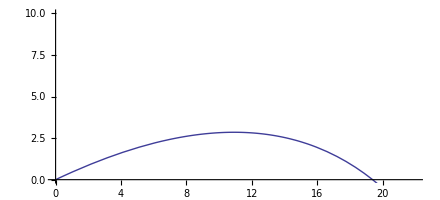

```mathematica
trajectory[25]
```

The range of the throw will be the distance the ball object goes before it hits the ground (y=0).  Use Manipulate to estimate at which angle the object should be thrown to have a maximum range.

HINT:  The correct answer is between 20 and 60 degrees.

Answer:

#### (#10) Manipulating Expressions (5 min)

The output of Manipulate need not be an expression.  For instance, evaluate the following expression and then change the slider to find a series expansion of the cosine function with orders from 1 to 15.

```mathematica
Manipulate[Series[Cos[x],{x,0,order}],{order,1,15,1}]
```

The probability of rolling a seven in a single roll of two dice P(1) is given by the number of ways to get a seven (6) divided by the total possible combinations of the two dice (36).  In other words, P(1)=1/6 .  The probability of rolling at at least one seven in two rolls P(2) is 1-[1-P(1)]^2,  since the probability of not rolling a seven in one roll is 1-P(1)  and the probability of not rolling a seven in either of two rolls is [1-P(1)]^2.   Extending this reasoning, the probability of rolling at least one seven in n rolls is 1-[1-P(1)]^n=1-(5/6)^n.  Manipulate an expression to find this probability as a function of n for n between 1 and 30 .

How many rolls do you need to make in order to have a 99% probability of getting at least one seven?

Answer:

### (#11) Animation (15 min)

Explore the DC reference pages for both Animate and ListAnimate, including a brief look at the More Information and Options sections of those pages.  These functions are redundant in that Manipulate can also do anything that they can do.  Animate and ListAnimate windows have simpler (i.e. more restricted) interfaces that appear to be tuned more for display than exploration.  And ListAnimate provides a convenient way to quickly animate the sequence of elements within any list.

a) Use Animate to create a graph showing the amplitude of a sound wave as a function of time for two complete periods and three wavelengths.  Use the equation of motion y(x,t)==2.5 cos(π x-2 π t) corresponding to a wave with an amplitude of 2.5, a wavelength of 2 and a frequency of one.

```mathematica
Animate[Plot[2.5 Cos[Pi x-2 Pi t],{x,0,6}, PlotRange->{All,{-2.6,2.6}}],{t,0,2}]
```

b) Use ListAnimate to animate the list of graphics objects below.  Then use the following options to modify the behavior of the animation: DefaultDuration, AnimationRate, AnimationDirection, AnimationRepetitions, AnimationRunning and ControlPlacement.

```mathematica
coordlist = Table[{x,2(1-x^2)},{x,-1,1,0.1}]
snapshot[xy_] := Graphics[{PointSize[0.05],Point[xy]},Frame->True,Axes->True,AxesOrigin->{-10,10},PlotRange->{{-1,1},{0,2}},ImageSize->200]
glist = snapshot/@coordlist
```

## Applications (40 min)

### (#12) Waves (15 min)

(a) Plot a travelling wave of the form A Cos[k x - ω t] over the x range from 0 to 10 meters, and Manipulate it over the t range from 0 to 10 seconds, where the amplitude A is 1.0, the wavevector k is 4.0 radians/meter, and the angular frequency ω is 2.0 radians/second.  Add a frame to the plot, label the axes as "x(meters)" and "amplitude", label the time slider as "t(seconds)", use PlotRange → {-2 A, 2 A}, and make sure that PlotPoints is high enough to ensure a smooth curve.  Demonstrate that the velocity at which the wave tips move (i.e. the phase velocity v_ϕ) is given by the expression  v_ϕ=ω/k, and that the direction of travel is determined by the sign of v_ϕ.

(b) Copy your code above into the cell below and modify it to illustrate two travelling waves (same wavevector and frequency) moving in opposite directions.

(c) Copy your code above into the cell below and modify it to illustrate that when the two waves are superposed (i.e. added together), the result is a standing wave.

(d) Evaluate the cell below, where we have superimposed two waves plotted as a function of time.  In this case, one of the waves has a fixed frequency and the other wave has a variable frequency.  What happens when the two wave frequencies are very similar?  Can you see a relationship between the "beat" frequency (or the beat period, T_beat = (2π)/ω_beat) and the frequencies of the individual wave components?

```mathematica
Manipulate[Plot[Cos[4 t] + Cos[ω t],{t,0,100},PlotPoints->200,ImageSize->600],{ω,2.5,5.5,0.1}]
```

### (#13) Projectile trajectory (15 min)

Use Manipulate to illustrate the motion of a projectile that is fired up and off the edge of a cliff.  The projectile should be fired up and to the right from the origin on a trajectory that has an initial slope of 2 and reaches a maximum height at x = 1.  The illustration should include the entire region from -3 to +3 along both the x and y axes.  Illustrate the cliff (everthing below and to the left of the origin) as a rectangle.

Hint:  You know that under the influence of gravity, the projectile will follow a parabolic (i.e. quadratic) trajectory.  With pencil and paper, start with a general quadratic of the form y=a+b x+c x^2, and apply the three boundary conditions provided {y(0) = 0, y'(0) = 2, y'(1) = 0} to solve for the coefficients.  Use the resulting quadratic to place the projectile at the correct Point as x varies from 0 to 3.

### (#14) 3D visualization (10 min)

Create a 3D graphic that includes a rectangular solid (Cuboid), an ellipsoid (Sphere) and a Cylinder.  Then Rotate the entire group of primitives by 45° around the z-axis.  Render the figure in Graphics3D with PlotRange → {{-2, 2}, {-2, 2}, {-2, 2}}, making sure that none of your primitives extend outside this region.

Now let the z-axis rotation angle be a variable and Animate its 360° rotation.  Because the animation automatically starts over each time it ends, the rotation appears to be continuous.  Try reorienting the spinning figure with your mouse.  Explain the result.

## Exporting Graphics (10 min)

When you make presentations or write publications you will frequently want to include graphics from Mathematica in other programs such as Word or PowerPoint.  In presentations, you may also want to create stand-alone animations so that you don’t need to have Mathematica running on the computer where you are presenting your data.

We will go into more details about importing and exporting general data, but this seems like a good place to discuss how to transfer graphical information from Mathematica to other programs.

### (#15) Exporting Graphs and Drawings (5 min)

There are two ways to exports graphical data with Mathematica.  The simplest way is to just copy and paste the graph from one program to another.  Practice that by clicking on the graph below and then pasting it into a new Microsoft Word document.

Evaluate the code in the following statement to create a graph.

Right-click on the graph to bring up a pop-up menu and select “Copy Graphic.”

Open a Word Document and select Paste from the Home Tab (or type Ctrl-V).

```mathematica
Plot[Pi*Exp[-x],{x,0,3}, PlotLabel->"Population Probability",AxesLabel->{t,P}]
```

Sometimes it is preferable to save the graphic in a file.  You can do this by selecting the graphic you are interested in (or some or all of the graphical elements in the graphic) and then using the File/Save Selection As... menu item.  There are a wide variety of file formats available in the Save As Type drop-down menu box on the screen which will pop up.

Save the above plot as a png file.

The final way to export graphics is using the Export command.  As you’ll note on the DC page, it normally takes two arguments.  The first is the name of the file and the second is the variable containing the Grahics Object.  Store the graphics object produced by the following command in a file named contour.bmp.  The SetDirectory command will ensure that this file is stored in the same directory as your Notebook.

```mathematica
SetDirectory[NotebookDirectory[]];
graphic=ContourPlot[10*Exp[-Sqrt[(x^2+y^2)]]*Cos[ArcTan[x,y]],{x,-2,2},{y,-3,3}, PlotRange->All];
```

### (#16) Exporting Animations (5 min)

Animations can also be exported, but the number of available file formats is limited.  First try exporting the following animation as the file wave.avi.  When you play it, note that the controls are visible as part of the animation, even though they are inactive.  (Be patient.  This will take a while since it is a large file.)

```mathematica
agraph = Animate[Plot[3*Cos[x-t/2],{x,0,2 Pi}],{t,0,4Pi}];
```

A faster way to create and store the graph is as a list of graphics objecrts which can then be exported.  Export this graph list to the file graphics.avi and then display it on your screen.  Note that it doesn’t waste as much space, doesn’t show the inactive control buttons, and is created a lot faster.  There are a number of free programs you can use outside of Mathematica to convert the avi file to compressed formats.

```mathematica
graphs = Table[Plot[3*Cos[x-t/2],{x,0, 2 Pi}], {t,0, 4 Pi, Pi/10}];
```

## On Your Own (30 min)

### (#17) Width and Location of Delta-Resonance (15 min)

The list resonance is measured cross section data of a reaction where a gamma ray strikes a proton and producesa π_0 particle.  It consists of pairs of numbers where the first number is the energy E measured in MeV (millions of electron Volts) and the second is the cross section σ measured in microbarns.  It was reported on the web site at http://jazz.physik.unibas.ch/~krusche/delta_Npi.html.  One would expect the shape of this cross section to have a roughly Lorentzian line shape with σ=A/((E-E_0)^2+w^2).  Find the graphical estimates for the values of A, E_0, and w usign the Manipulate function.

HINT:  Plot a graph of the data to get initial estimates for the parameters you are estimating.  Looking at the equation for the cross section, you should be able to estimate at which value of E the function will have its maximum value.  You will also note that the function will have half of its maximum value when E-E_0=w.  This should allow you to estimate w from the graph.  The highest point will then have an amplitude of the maximum value of the data times w^2.

```mathematica
SetDirectory[NotebookDirectory[]]
resonance=Import["gammapi.csv"];
```

### (#18) (15 min)

Create an unscaled solar system model with a yellow disk representing the Sun, a blue disk representing the Earth, and a Gray disk representing the Moon.  The Earth should orbit the Sun once a year and the moon should orbit the Earth every 28 days.  If you put the sun at the origin, the position of the Earth is x_E=r_E cos(t ω_E) and y_E=r_E sin(t ω_E), where ω is the rotation speed of the Earth in radians per day and t is in days.  The location of the Moon will have a similar form, relative to the center of the Earth.  Thus its position is x_M=r_M cos(t ω_M)+x_ⅇ and y_M=r_M sin(t ω_M)+y_E, where ω_M  is the angular speed of the Moon around the Earth in radians per day.  Use reasonable values for the sizes of the Sun, Moon, and Earth and their orbits so the animation is easy to see.  Have the animation go for a full year.